```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/Teukolsky.wl"
<<"Definitions/SWSH.wl"
```

## NP decomposition in right/left polarizations

```mathematica
F=({{0, 0, r Eθ, r Sin[θ]Eϕ}, {0, 0, -r Bϕ, r Sin[θ]Bθ}, {-r Eθ, r Bϕ, 0, 0}, {-r Sin[θ]Eϕ, -r Sin[θ]Bθ, 0, 0}});
```

```mathematica
η=DiagonalMatrix[{1,-1,-r^2,r^2Sin[θ]^2}]
```

{{1,0,0,0},{0,-1,0,0},{0,0,-r^2,0},{0,0,0,r^2 Sin[θ]^2}}

```mathematica
l={1,1,0,0};
n={1,-1,0,0}/2;
m={0,0,1,I Csc[θ]}/(r Sqrt[2]);
```

```mathematica
l.F.m/.Join@@Thread/@{{Eθ,Eϕ}->{ℰ eθ,ℰ eϕ},{Bθ,Bϕ}->{ℬ eθ,ℬ eϕ}}//FullSimplify[#,{r,θ}∈Reals]&
```

((eθ+ⅈ eϕ) (ⅈ ℬ+ℰ))/(√2)

```mathematica
Conjugate[m].F.n/.Join@@Thread/@{{Eθ,Eϕ}->{ℰ eθ,ℰ eϕ},{Bθ,Bϕ}->{ℬ eθ,ℬ eϕ}}//FullSimplify[#,{r,θ}∈Reals]&
```

-((ⅈ eθ+eϕ) (ℬ-ⅈ ℰ))/(2 √2)

```mathematica
e[0]={Sin[θ0]Cos[ϕ0],Sin[θ0]Sin[ϕ0],Cos[θ0]};
e[1]={Sin[ϕ0],-Cos[ϕ0],0};
e[2]={Cos[θ0]Cos[ϕ0],Cos[θ0]Sin[ϕ0],-Sin[θ0]};
e[ϕ]=-{Sin[ϕ],-Cos[ϕ],0};
e[θ]={Cos[θ]Cos[ϕ],Cos[θ]Sin[ϕ],-Sin[θ]};
```

```mathematica
fieldDecomp={ℰ->1/2(Exp[-I ω t+I k.r](ϵ1 e[1]+ϵ2 e[2])+Exp[I ω t-I k.r](ϵ1*e[1]+ϵ2*e[2])),ℬ->1/2(Exp[-I ω t+I k.r](ϵ1 e[2]-ϵ2 e[1])+Exp[I ω t-I k.r](ϵ1*e[2]-ϵ2*e[1]))};
RuleLR={ϵ1->√2(ϵL+ϵR)/2,ϵ2->-I √2(ϵL-ϵR)/2};
```

```mathematica
Φ0=((ⅈ ℬ+ℰ).(e[θ]+ⅈ e[ϕ]))/(√2)/.fieldDecomp//FullSimplify;
```

```mathematica
Φ2=-((ⅈ ℬ+ℰ).(e[θ]-ⅈ e[ϕ]))/(2 √2)/.fieldDecomp//FullSimplify;
```

```mathematica
Φ0/ComplexExpand@Sum[SpinWeightedSphericalHarmonicY[-1,1,m,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[1,1,m,θ,ϕ],{m,-1,1}]//Collect[#/.RuleLR//FullSimplify//Factor,Exp[_]]&
```

-4/3 ⅈ ⅇ^(-ⅈ t ω+ⅈ k.r) π ϵR-4/3 ⅈ ⅇ^(ⅈ t ω-ⅈ k.r) π Conjugate[ϵL]

```mathematica
Φ2/ComplexExpand@Sum[SpinWeightedSphericalHarmonicY[-1,1,m,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[-1,1,m,θ,ϕ],{m,-1,1}]//Collect[#/.RuleLR//FullSimplify//Factor,Exp[_]]&
```

-2/3 ⅈ ⅇ^(-ⅈ t ω+ⅈ k.r) π ϵR-2/3 ⅈ ⅇ^(ⅈ t ω-ⅈ k.r) π Conjugate[ϵL]

## Plane wave decomposition in spherical harmonics

```mathematica
ϕ2DecompCoef[𝓈_,𝒿_,ℓ_]=((2𝓈+1)(2ℓ+1))/(2𝒿+1)Abs[ClebschGordan[{ℓ,0},{𝓈,𝓈},{𝒿,𝓈}]]^2//FullSimplify[#,{{𝓈,ℓ,𝒿}∈Integers}]&//(#/.Gamma[n_]:>Factorial[n-1])&
```

Piecewise[{{((1+2 ℓ) (𝒿+ℓ-𝓈)! (𝒿+𝓈)! (1+2 𝓈)!)/((𝒿-𝓈)! (𝒿-ℓ+𝓈)! (-𝒿+ℓ+𝓈)! (1+𝒿+ℓ+𝓈)!), 𝒿≥𝓈&&𝒿≤ℓ+𝓈&&𝒿+𝓈≥ℓ}, {0, True}}]

```mathematica
ϕ0DecompCoef[𝓈_,𝒿_,ℓ_]=((2𝓈+1)(2ℓ+1))/(2𝒿+1)ClebschGordan[{ℓ,0},{𝓈,-𝓈},{𝒿,-𝓈}]*ClebschGordan[{ℓ,0},{𝓈,𝓈},{𝒿,𝓈}]//FullSimplify[#,{{𝓈,ℓ,𝒿}∈Integers}]&//(#/.Gamma[n_]:>Factorial[n-1])&
```

Piecewise[{{((-1)^(𝒿+ℓ+𝓈) (1+2 ℓ) (𝒿+ℓ-𝓈)! (𝒿+𝓈)! (1+2 𝓈)!)/((𝒿-𝓈)! (𝒿-ℓ+𝓈)! (-𝒿+ℓ+𝓈)! (1+𝒿+ℓ+𝓈)!), 𝒿≤ℓ+𝓈&&𝒿+𝓈≥ℓ&&𝒿≥𝓈}, {0, True}}]

### ϵ_R

```mathematica
coef2=(∑_(ℓ=𝒿-1)^(𝒿+1) ϕ2DecompCoef[1,𝒿,ℓ] ⅈ^ℓ SphericalBesselJ[ℓ,x])//Simplify[#,𝒿≥1]&//TrigToExp@Normal@Series[#,{x,∞,3}]&//(-I/3)*FullSimplify[Coefficient[ExpandAll[#]/.{Gamma[a_]:>Factorial[a-1],x->ω r},{Exp[I ω r]/r,Exp[-I ω r]/r^3}],𝒿∈Integers]&
```

{-1/(2 ω),((-1)^𝒿 𝒿 (1+𝒿))/(8 ω^3)}

```mathematica
coef0=(∑_(ℓ=𝒿-1)^(𝒿+1) ϕ0DecompCoef[1,𝒿,ℓ] ⅈ^ℓ SphericalBesselJ[ℓ,x])//Simplify[#,𝒿≥1]&//TrigToExp@Normal@Series[#,{x,∞,3}]&//(-I/3)*FullSimplify[Coefficient[ExpandAll[#]/.{Gamma[a_]:>Factorial[a-1],x->ω r},{Exp[-I ω r]/r,Exp[I ω r]/r^3}],𝒿∈Integers]&
```

{-(-1)^𝒿/(2 ω),(𝒿 (1+𝒿))/(8 ω^3)}

### ϵ_L*

```mathematica
(∑_(ℓ=𝒿-1)^(𝒿+1) ϕ2DecompCoef[1,𝒿,ℓ] ⅈ^ℓ SphericalBesselJ[ℓ,x])*//Simplify[#,𝒿≥1]&//TrigToExp@Normal@Series[#,{x,∞,3}]&//FullSimplify[#,{𝒿∈Integers,x∈Reals}]&//-(I/3)*FullSimplify[Coefficient[ExpandAll[#]/.{Gamma[a_]:>Factorial[a-1],x->ω r},{Exp[-I ω r]/r,Exp[I ω r]/r^3}],𝒿∈Integers]&
```

{1/(2 ω),-((-1)^𝒿 𝒿 (1+𝒿))/(8 ω^3)}

```mathematica
(∑_(ℓ=𝒿-1)^(𝒿+1) ϕ0DecompCoef[1,𝒿,ℓ] ⅈ^ℓ SphericalBesselJ[ℓ,x])*//Simplify[#,𝒿≥1]&//TrigToExp@Normal@Series[#,{x,∞,3}]&//FullSimplify[#,{𝒿∈Integers,x∈Reals}]&//-(I/3)*FullSimplify[Coefficient[ExpandAll[#]/.{Gamma[a_]:>Factorial[a-1],x->ω r},{Exp[I ω r]/r,Exp[-I ω r]/r^3}],𝒿∈Integers]&
```

{(-1)^𝒿/(2 ω),-(𝒿 (1+𝒿))/(8 ω^3)}

## Dipolar Field

```mathematica
mP=m0/2 ((Sin[α]Exp[-I ω t]({1,0,0}+ζ I{0,1,0}))+Cos[α]{0,0,1})//ComplexExpand
```

{1/2 m0 Cos[t ω] Sin[α]-1/2 ⅈ m0 Sin[α] Sin[t ω],1/2 ⅈ m0 ζ Cos[t ω] Sin[α]+1/2 m0 ζ Sin[α] Sin[t ω],1/2 m0 Cos[α]}

```mathematica
X={x,y,z};
XS={xS,yS,zS};
RuleSphericalS={zS->Cos[θS]L,yS->Sin[θS]Sin[ϕS]L,xS->Sin[θS]Cos[ϕS]L};
RuleChangeDirection={θS->π-θ0,ϕS->ϕ0+π};
p=-ω Normalize[XS]//ComplexExpand;
```

```mathematica
DipF=μ0/(8Pi)Exp[I ω Norm[XS]]/Norm[XS] Exp[-I ω Normalize[XS].X]Cross[-Normalize[XS],D[mP, {t,2}]]/.RuleSphericalS//ComplexExpand//Simplify[#,L>0]&;
```

```mathematica
DipFn=(DipF/Exp[-I ω t+I p.X]/.RuleSphericalS)//ComplexExpand//FullSimplify[#,L>0]&
```

{-(ⅈ ⅇ^(ⅈ L ω) m0 ζ μ0 ω^2 Cos[θS] Sin[α])/(16 L π),(ⅇ^(ⅈ L ω) m0 μ0 ω^2 Cos[θS] Sin[α])/(16 L π),(ⅈ ⅇ^(ⅈ L ω) m0 μ0 ω^2 Sin[α] Sin[θS] (ζ Cos[ϕS]+ⅈ Sin[ϕS]))/(16 L π)}

```mathematica
E1=Simplify[2DipFn.{-Sin[ϕS],Cos[ϕS],0}/.RuleChangeDirection]//.{α_ Cos[x_]+β_.Sin[x_]->α(Cos[x]+β/α Sin[x]),ζ^n_:> ζ^Mod[n,2],Cos[x_]+Complex[0,α_]z_.Sin[x_]:>Exp[I z α x]/;z==1||z==ζ}
```

(ⅇ^(ⅈ ζ ϕ0+ⅈ L ω) m0 μ0 ω^2 Cos[θ0] Sin[α])/(8 L π)

```mathematica
E2=Simplify[2 DipFn.{Cos[θS]Cos[ϕS],Cos[θS]Sin[ϕS],-Sin[θS]}/.RuleChangeDirection]//.{α_ Cos[x_]+β_.Sin[x_]:>α(Cos[x]+β/α Sin[x]),ζ^n_:> ζ^Mod[n,2],Cos[x_]+Complex[0,α_]z_.Sin[x_]:>Exp[I z α x]/;z==1||z==ζ}
```

(ⅈ ⅇ^(ⅈ ζ ϕ0+ⅈ L ω) m0 ζ μ0 ω^2 Sin[α])/(8 L π)

```mathematica
{EL,ER}={E1+I E2,E1-I E2}/√2;
```

```mathematica
Table[{Simplify[EL*,{α,ω,μ0,m0,ϕ0,θ0,L}∈Reals]/(ζ SpinWeightedSphericalHarmonicY[-1,1,-ζ,θ0,ϕ0]),ER/(-ζ SpinWeightedSphericalHarmonicY[-1,1,ζ,θ0,ϕ0])},{ζ,{-1,1}}]ᵀ//Simplify
```

{{(ⅇ^(-ⅈ L ω) m0 μ0 ω^2 Sin[α])/(2 L √(6 π)),(ⅇ^(-ⅈ L ω) m0 μ0 ω^2 Sin[α])/(2 L √(6 π))},{(ⅇ^(ⅈ L ω) m0 μ0 ω^2 Sin[α])/(2 L √(6 π)),(ⅇ^(ⅈ L ω) m0 μ0 ω^2 Sin[α])/(2 L √(6 π))}}

## Scattering

```mathematica
ϕ2plane=2 Pi ϵR Exp[-I ω t](-1/(2ω)Exp[I ω rs]/r+(-1)^ℓ(ℓ(ℓ+1))/(8 ω^3)Exp[-I ω rs]/r^3)Y[-1,ℓ,𝓂,θ0,ϕ0]*Y[-1,ℓ,𝓂,θ,ϕ]*
```

2 ⅇ^(-ⅈ t ω) π ϵR (((-1)^ℓ ⅇ^(-ⅈ rs ω) ℓ (1+ℓ))/(8 r^3 ω^3)-ⅇ^(ⅈ rs ω)/(2 r ω)) Conjugate[Y[-1,ℓ,𝓂,θ,ϕ]] Conjugate[Y[-1,ℓ,𝓂,θ0,ϕ0]]

```mathematica
ϕ2scat=2 Pi ϵR Exp[-I ω t]((-1)^ℓ ℓ (1+ℓ))/(8 Zin ω^3)(Zout Exp[I ω rs]/r+Zin Exp[-I ω rs]/r^3)Y[-1,ℓ,𝓂,θ0,ϕ0]*Y[-1,ℓ,𝓂,θ,ϕ]*
```

((-1)^ℓ ⅇ^(-ⅈ t ω) π ((ⅇ^(-ⅈ rs ω) Zin)/r^3+(ⅇ^(ⅈ rs ω) Zout)/r) ℓ (1+ℓ) ϵR Conjugate[Y[-1,ℓ,𝓂,θ,ϕ]] Conjugate[Y[-1,ℓ,𝓂,θ0,ϕ0]])/(4 Zin ω^3)

```mathematica
(ϕ2scat-ϕ2plane)/((2 Pi ϵR)/(-2 ω)Exp[-I ω t +I ω rs]/r Conjugate[Y[-1,ℓ,𝓂,θ,ϕ]] Conjugate[Y[-1,ℓ,𝓂,θ0,ϕ0]])//Limit[#,r->∞]&//Expand//Simplify
```

-1+((-1)^ℓ Zout ℓ (1+ℓ))/(4 Zin ω^2)

## Plots

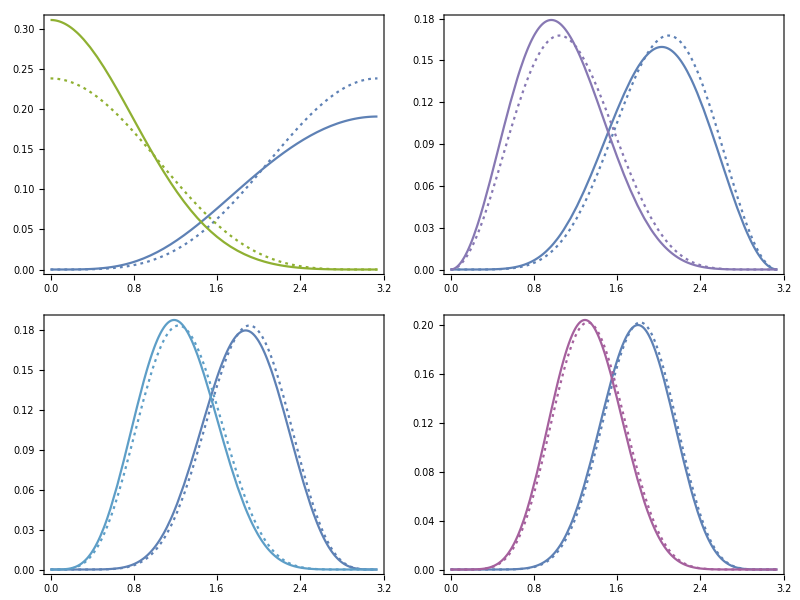

```mathematica
{Plot[{Style[SpinWeightedSpheroidalHarmonicS[-1,1,#,0,θ,0]^2,Directive[Dashing[{2,3}/500.],ColorData[97,2+#]]],Style[SpinWeightedSpheroidalHarmonicS[-1,1,#,0.5,θ,0]^2,ColorData[97,2+#]]}&/@{-1,1}//Flatten//Evaluate,{θ,0,π},PlotRange->All,Frame->True],
Plot[{Style[SpinWeightedSpheroidalHarmonicS[-1,2,#,0,θ,0]^2,Directive[Dashing[{2,3}/500.],ColorData[97,3+#]]],Style[SpinWeightedSpheroidalHarmonicS[-1,2,#,0.5,θ,0]^2,ColorData[97,3+#]]}&/@{-2,2}//Flatten//Evaluate,{θ,0,π},PlotRange->All,Frame->True],
Plot[{Style[SpinWeightedSpheroidalHarmonicS[-1,3,#,0,θ,0]^2,Directive[Dashing[{2,3}/500.],ColorData[97,4+#]]],Style[SpinWeightedSpheroidalHarmonicS[-1,3,#,0.5,θ,0]^2,ColorData[97,4+#]]}&/@{-3,3}//Flatten//Evaluate,{θ,0,π},PlotRange->All,Frame->True],
Plot[{Style[SpinWeightedSpheroidalHarmonicS[-1,4,#,0,θ,0]^2,Directive[Dashing[{2,3}/500.],ColorData[97,5+#]]],Style[SpinWeightedSpheroidalHarmonicS[-1,4,#,0.5,θ,0]^2,ColorData[97,5+#]]}&/@{-4,4}//Flatten//Evaluate,{θ,0,π},PlotRange->All,Frame->True]}//Grid[Partition[(Show[#,ImageSize->500]&)/@#,2,2,{1,1},SpanFromLeft]]&
```